```mathematica
raw=Drop[Import[FileNameJoin[{NotebookDirectory[],"data/out.dat"}], "Table", "FieldSeparators"->{" "}, HeaderLines->1], -1];
```

```mathematica
cdata=Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]]}];
vdata=Transpose[{raw[[All, 12]], raw[[All, 13]], raw[[All, 14]]}];
pdata=raw[[All, 16]];
```

```mathematica
avgv=Mean[Sqrt[vdata[[All, 1]]^2+vdata[[All,2]]^2+vdata[[All, 3]]^2]]
```

0.00163126

```mathematica
maxv=Max[Abs[vdata]]
```

0.030812

```mathematica
l=Abs[Max[Flatten[cdata]]-Min[Flatten[cdata]]]
```

2.

```mathematica
ren=avgv*l/0.000890
```

3.66576

```mathematica
maxren=maxv*l/0.000890
```

69.2404

```mathematica
arrows=Table[{Arrowheads[.01],Arrow[{
cdata[[i]],cdata[[i]]+
(vdata[[i]]/(maxv))*l*0.2
}]}, {i, Length[raw]}];
```

```mathematica
gg=Graphics3D[arrows,Axes->True,AxesLabel->{"x (m)","y (m)","z (m)"},ImageSize->Large]
```

-Graphics3D-

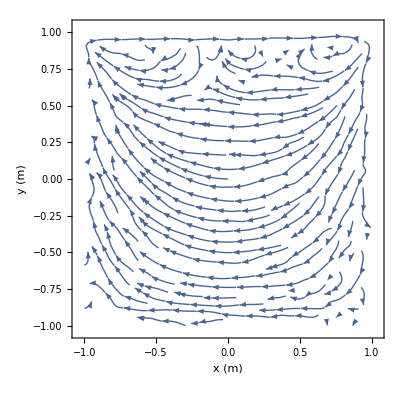

```mathematica
ListStreamPlot[Table[{{cdata[[i, 1]], cdata[[i, 2]]}, {vdata[[i, 1]], vdata[[i, 2]]}}, {i, Length[vdata]}], FrameLabel->{"x (m)","y (m)"}]
```

```mathematica
(*ListContourPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}], PlotRange->All, PlotLegends->Automatic]*)
```

```mathematica
ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}],ColorFunction->"TemperatureMap",PlotLegends->BarLegend[All, LegendLabel->"p (Pa)"], PlotRange->All,AxesLabel->{"x (m)","y (m)","z (m)"}]
```

-Graphics3D-

```mathematica
(*ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], Sqrt[raw[[All, 12]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2]}],ColorFunction->"BlueGreenYellow",PlotLegends->Automatic, PlotRange->All]*)
```

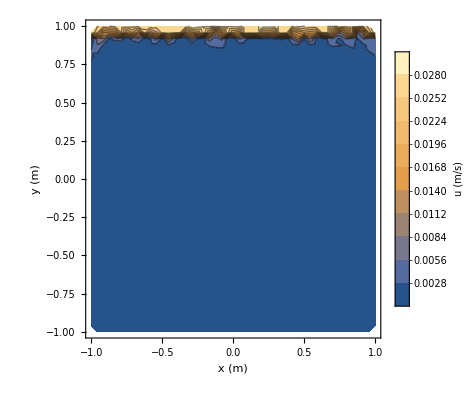

```mathematica
vmp=ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], Sqrt[raw[[All, 12]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2]}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"u (m/s)"], Contours->10, FrameLabel->{"x (m)", "y (m)"}]
```

```mathematica
Export["~/Dropbox/contour_vm.pdf", vmp]
```

~/Dropbox/contour_vm.pdf

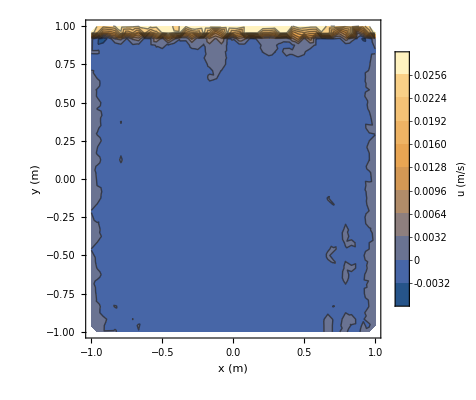

```mathematica
vxp=ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 12]]}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"u (m/s)"], Contours->10, FrameLabel->{"x (m)", "y (m)"}]
```

```mathematica
Export["~/Dropbox/contour_vx.pdf", vxp]
```

~/Dropbox/contour_vx.pdf

```mathematica
c1=ImportString["\
itn 1 / 10, res 9.0905e-02
itn 2 / 10, res 4.1792e-02
itn 3 / 10, res 3.4106e-02
itn 4 / 10, res 2.2165e-02
itn 5 / 10, res 1.3975e-02
itn 6 / 10, res 1.0517e-02
itn 7 / 10, res 8.4571e-03
itn 8 / 10, res 7.5083e-03
itn 9 / 10, res 6.8457e-03
itn 10 / 10, res 6.2835e-03
", "Table", "FieldSeparators"->{" "}][[All, 6]];
```

```mathematica
c1fit=Fit[c1, {1, x, 1/x}, x]
```

-0.000375578+0.0915338/x-0.000396169 x

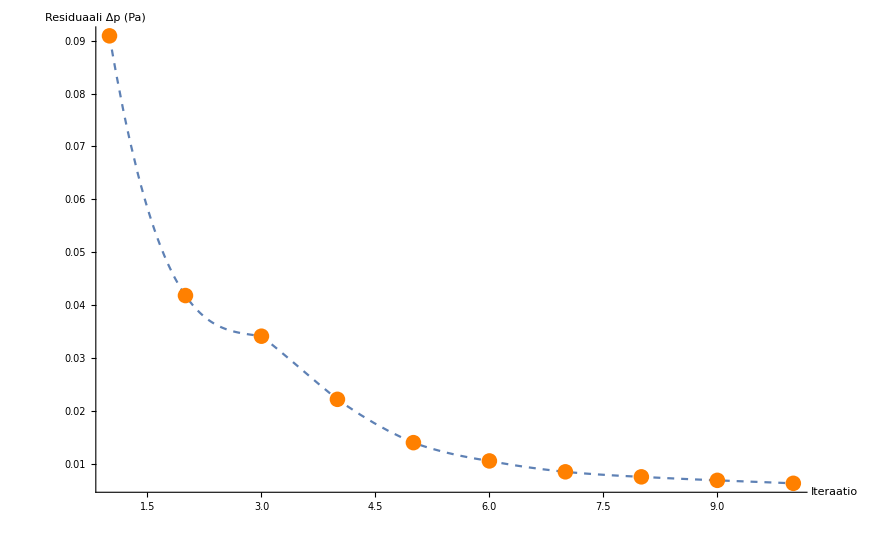

```mathematica
Show[(*Plot[c1fit, {x, 1, Length[c1]}, PlotStyle->LightGray, PlotRange->All],*)Plot[Interpolation[c1][x], {x, 1, Length[c1]}, PlotStyle->Dashed, PlotRange->All], ListPlot[c1, PlotStyle->Orange], AxesLabel->{"Iteraatio", "Residuaali Δp (Pa)"}, PlotRange->All, AxesOrigin->{1,0}]
```